6

{1.,1.1,1.2,1.3,1.4,1.5}

{0,-0.111502,-0.253884,-0.445626,-0.722859,-1.16778}

1. | 0 |  |  |  |  |  | 
1.1 | -0.111502 | -0.1 | -0.0247136 | -0.0135749 | -0.0112775 |  | 
1.2 | -0.253884 | -0.124714 | -0.0382885 | -0.0248524 |  |  | 
1.3 | -0.445626 | -0.163002 | -0.0631409 |  |  |  | 
1.4 | -0.722859 | -0.226143 |  |  |  |  | 
 |  |  |  |  |  |  | 
 |  |  |  |  |  |  | 
 |  |  |  |  |  |  | 
 |  |  |  |  |  |  | 
 |  |  |  |  |  |  | 
 |  |  |  |  |  |  | 
 |  |  |  |  |  |  |

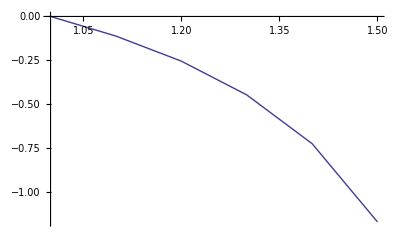

```mathematica
f[x_,y_]:=-(x^2 y^2-(2x+1)y + 1)/x;
y0=0;
a=1;
b=1.5;
h=0.1;
X=Range[a,b,h];
n=Length[X];
Print[n];
Print[X];
Y=Table[{},{n}];
K1=Table[{},{n}];
K2=Table[{},{n}];
K3=Table[{},{n}];
K4=Table[{},{n}];
Y[[1]]=y0;
For[i=2,i≤n,i++,
K1[[i]] = h f[X[[i-1]],Y[[i-1]]];
K2[[i]]  =  h f[X[[i-1]] + h/2,Y[[i-1]] + K1[[i]] /2];
K3[[i]]  =  h f[X[[i-1]] + h/2,Y[[i-1]] + K2[[i]] /2];
K4[[i]]  =  h f[X[[i-1]] + h,Y[[i-1]] + K3[[i]] ];
delta = 1/6(K1[[i]]  + 2 K2[[i]]  + 2 K3[[i]] + K4[[i]] );
Y[[i]]=Y[[i-1]]+delta;
];
Print[Y];
NN=Table[{},{2n},{n+2}];
For[i=1,i≤5,i++,
NN[[i,1]]=X[[i]];
NN[[i,2]]=Y[[i]];
NN[[i,3]]=K1[[i]];
];
For[i=4,i≤n+2,i++,
For[j=1,j≤n-(i-3),j++,   (*?????????*)
NN[[j,i]]=NN[[j+1,i-1]]-NN[[j,i-1]];
]
];
Print[NN//TableForm];
dots=Table[{},{n}];
For[i=1,i≤n,i++,
dots[[i]]={X[[i]],Y[[i]]};
]
ListLinePlot[dots]
```

11

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

{{},-1.,-1.01608,-1.04437,-1.08616,-1.14285,-1.21601,-1.30737,-1.41883,-1.5525,-1.7107}

{{},0.9,0.814322,0.73682,0.666713,0.603294,0.545922,0.494019,0.447064,0.404583,0.366148}

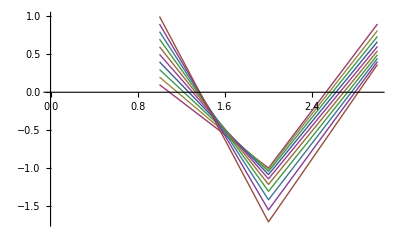

```mathematica
f1[x_,y_,z_]:=1-1/z;(*y'*)
f2[x_,y_,z_]:=1/(y-x); (*z'*)
y0=-1;
z0=1;
a=0;
b=1;
h=0.1;
(*n=(b-a)/h+1;*)
X=Range[a,b,h];
n=Length[X];
Print[n];
Print[X];
Y=Table[{},{n}];
Z=Table[{},{n}];
Y2=Table[{},{n}];
Z2=Table[{},{n}];
Y2[[1]]=y0;
Z2[[1]]=z0;
For[i=2,i≤n,i++,
Y[[i]]=Y2[[i-1]]+h*f1[X[[i-1]],Y2[[i-1]],Z2[[i-1]]];
Z[[i]]=Z2[[i-1]]+h*f2[X[[i-1]],Y2[[i-1]],Z2[[i-1]]];
Y2[[i]]=Y2[[i-1]]+h*(f1[X[[i-1]],Y2[[i-1]],Z2[[i-1]]]+f1[X[[i]],Y[[i]],Z[[i]]])/2;
Z2[[i]]=Z2[[i-1]]+h*(f2[X[[i-1]],Y2[[i-1]],Z2[[i-1]]]+f2[X[[i]],Y2[[i]],Z[[i]]])/2;
];
Print[Y];
Print[Z];
dots=Table[{},{n}];
For[i=1,i≤n,i++,
dots[[i]]={X[[i]],Y[[i]],Z[[i]]};
]
ListLinePlot[dots]
```